# Optics Preview – Zeroth Order (no variational correction)

Dry run of the paper' s full figure pipeline using ONLY single - particle energies (analytic, instant) . Purpose : shake down every plot before the production data lands, and expose what the zeroth order CANNOT provide . Findings so far : (1) the biexciton binding energy vanishes identically at zeroth order (E (XXijkl) = E (Xij) + E (Xkl)), so everything dividing by Ebind -- the two - photon chi3 -- needs the variational correction or a placeholder; (2) electron and hole orbitals share the same omega00 basis, so the interband dipole < psi_e | psi_h > = delta_ (state) : only X00 is bright from the ground state at zeroth order, and the oscillator strength of the excited transitions is entirely a correlation effect; (3) linewidths are phenomenological inputs we must choose . Energies are confinement energies (add the gap Eg for absolute photon energies) .

## Load definitions

```mathematica
dir = NotebookDirectory[];
Get[FileNameJoin[{ParentDirectory[dir, 3], "shared", "numerics", "definitions.wl"}]];
```

```mathematica
(* optional: overlay computed corrections where production results exist *)
useCorrections = False;
prodFile = FileNameJoin[{ParentDirectory[dir], "01-numerics", "production-results.wxf"}];
prodResults = If[useCorrections && FileExistsQ[prodFile],
   Import[prodFile, "WXF"], <||>];
```

## Zeroth-order energies

```mathematica
(* particle levels; lvl[2] shown for the extended diagram only *)
lvl[0] = {1, 0, 0}; lvl[1] = {1, 0, 1}; lvl[2] = {1, 1, 0};

e0X[a_, c_][i_, j_] := Ee[a, c, 0] @@ lvl[i] + Eh[a, c, 0] @@ lvl[j];
e0XX[a_, c_][i_, j_, k_, l_] :=
  Ee[a, c, 0] @@ lvl[i] + Ee[a, c, 0] @@ lvl[j] +
  Eh[a, c, 0] @@ lvl[k] + Eh[a, c, 0] @@ lvl[l];

(* meV throughout the plots *)
xMeV[a_, c_][i_, j_] := ER2meV e0X[a, c][i, j];
xxMeV[a_, c_][i_, j_, k_, l_] := ER2meV e0XX[a, c][i, j, k, l];
```

## Figure 1 analog: biexciton level diagram, two geometry sets

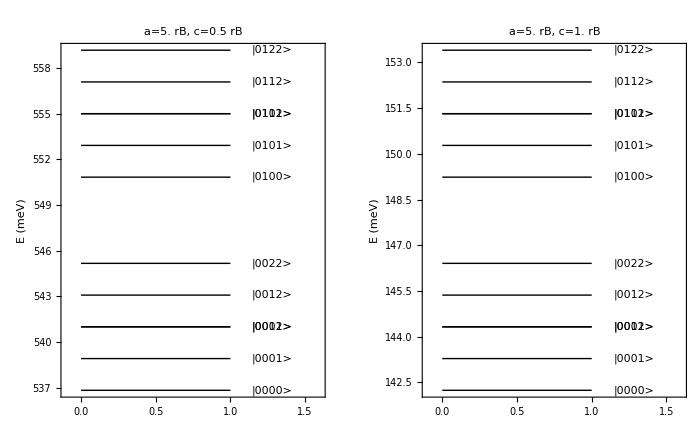

```mathematica
xxConfigs = DeleteDuplicates[
   Flatten[Table[{i, j, k, l}, {i, 0, 2}, {j, i, 2}, {k, 0, 2}, {l, k, 2}],
    3]];

levelDiagram[a_, c_, nLevels_: 12] :=
  Module[{lev},
   lev = SortBy[{xxMeV[a, c] @@ #, #} & /@ xxConfigs, First][[;; nLevels]];
   Graphics[{
     Table[{Thick,
       Line[{{0, lev[[n, 1]]}, {1, lev[[n, 1]]}}],
       Text[Style["|" <> StringJoin[ToString /@ lev[[n, 2]]] <> ">", 11],
        {1.28, lev[[n, 1]]}]}, {n, Length[lev]}]},
    Frame -> {{True, False}, {False, False}},
    FrameLabel -> {None, "E (meV)"},
    PlotLabel -> "a=" <> ToString[a] <> " rB,  c=" <> ToString[c] <> " rB",
    PlotRange -> {{-0.1, 1.6}, All}, AspectRatio -> 1.4, ImageSize -> 320]];

GraphicsRow[{levelDiagram[5.0, 0.5], levelDiagram[5.0, 1.0]},
 ImageSize -> 700]
```

## Figure 2 analog: transition scheme at the base geometry

```mathematica
(* the three exciton and three biexciton states of the paper's scheme;
   at zeroth order E(XX) - E(X) collapses to another exciton energy --
   the correction is what will split these lines *)
transitionTable[a_, c_] := Dataset[{
   <|"level" -> "X00", "E (meV)" -> xMeV[a, c][0, 0]|>,
   <|"level" -> "X01", "E (meV)" -> xMeV[a, c][0, 1]|>,
   <|"level" -> "X10", "E (meV)" -> xMeV[a, c][1, 0]|>,
   <|"level" -> "XX0000", "E (meV)" -> xxMeV[a, c][0, 0, 0, 0]|>,
   <|"level" -> "XX0001", "E (meV)" -> xxMeV[a, c][0, 0, 0, 1]|>,
   <|"level" -> "XX0100", "E (meV)" -> xxMeV[a, c][0, 1, 0, 0]|>,
   <|"level" -> "XX0000 -> X00",
    "E (meV)" -> xxMeV[a, c][0, 0, 0, 0] - xMeV[a, c][0, 0]|>,
   <|"level" -> "XX0001 -> X01",
    "E (meV)" -> xxMeV[a, c][0, 0, 0, 1] - xMeV[a, c][0, 1]|>,
   <|"level" -> "XX0100 -> X10",
    "E (meV)" -> xxMeV[a, c][0, 1, 0, 0] - xMeV[a, c][1, 0]|>}];
transitionTable[5.0, 0.5]
```

## Geometry scans (continuous at zeroth order)

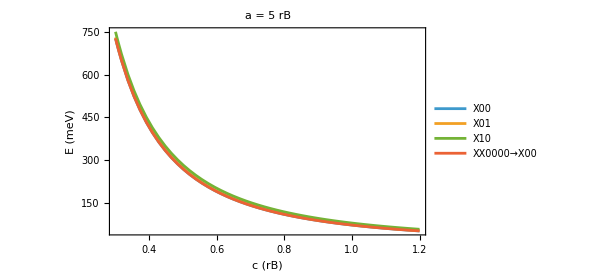

```mathematica
(* transition energies vs the small semiaxis at a = 5 *)
Plot[{xMeV[5.0, c][0, 0], xMeV[5.0, c][0, 1], xMeV[5.0, c][1, 0],
  xxMeV[5.0, c][0, 0, 0, 0] - xMeV[5.0, c][0, 0]},
 {c, 0.3, 1.2}, Frame -> True,
 FrameLabel -> {"c (rB)", "E (meV)"},
 PlotLegends -> {"X00", "X01", "X10", "XX0000→X00"},
 PlotLabel -> "a = 5 rB", ImageSize -> 450]
```

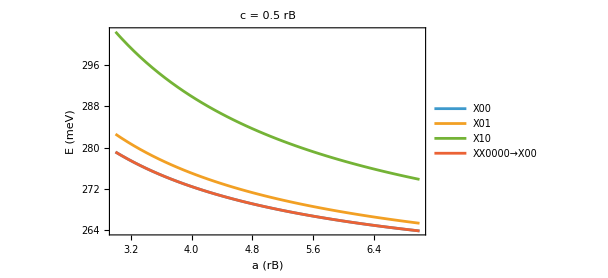

```mathematica
(* and vs the large semiaxis at c = 0.5 *)
Plot[{xMeV[a, 0.5][0, 0], xMeV[a, 0.5][0, 1], xMeV[a, 0.5][1, 0],
  xxMeV[a, 0.5][0, 0, 0, 0] - xMeV[a, 0.5][0, 0]},
 {a, 3, 7}, Frame -> True,
 FrameLabel -> {"a (rB)", "E (meV)"},
 PlotLegends -> {"X00", "X01", "X10", "XX0000→X00"},
 PlotLabel -> "c = 0.5 rB", ImageSize -> 450]
```

## Dipoles and selection rules at zeroth order

```mathematica
(* interband dipole ~ <psi_e|psi_h>: electron and hole orbitals come from
   the SAME omega00 basis, so the overlap is exactly delta_(state).
   Numeric confirmation via the radial overlap: *)
radialOverlap[a_, c_][{n1_, m1_}, {n2_, m2_}] :=
  If[m1 =!= m2, 0.,
   2 Pi NIntegrate[
     ψr[n1, m1][ℏω00[a, c], r] ψr[n2, m2][ℏω00[a, c], r] r,
     {r, 0, 0.9 a 5}]];
Dataset[{
  <|"pair" -> "e(0,0)-h(0,0)",
   "overlap" -> radialOverlap[5.0, 0.5][{0, 0}, {0, 0}]|>,
  <|"pair" -> "e(0,0)-h(0,1)",
   "overlap" -> radialOverlap[5.0, 0.5][{0, 0}, {0, 1}]|>,
  <|"pair" -> "e(0,0)-h(1,0)",
   "overlap" -> radialOverlap[5.0, 0.5][{0, 0}, {1, 0}]|>}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.001242}. NIntegrate obtained 6.93889×10^-18 and 3.09684×10^-12 for the integral and error estimates.

CONSEQUENCE: at zeroth order only ground -> X00 (and the ladder X00 -> XX0000, X01 -> XX0001, X10 -> XX0100, each adding a matching e-h pair) carry oscillator strength; ground -> X01 / X10 are dark. Any nonzero strength for the excited transitions in the final paper must come from the correlated wavefunctions -- the optics derivation has to evaluate dipole matrix elements over Psi = Psi0 F, not over Psi0.

## chi3 and absorption preview (placeholder response model)

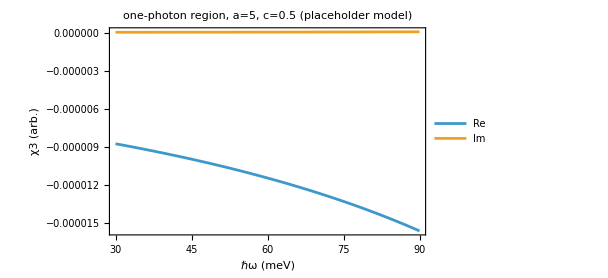

```mathematica
(* PREVIEW ONLY: standard three-level (ground / X / XX) Lorentzian response
   with unit dipoles; the real formulas come from the optics derivation.
   Ebind = 0 at zeroth order -> the two-photon chi3 ~ 1/Ebind^2 is singular;
   ebindPh (meV) is a placeholder -- replace with 2E(X00) - E(XX0000) from
   production-results.wxf when available. *)
gam = 0.5;      (* hbar*Gamma, meV, phenomenological *)
ebindPh = 1.0;  (* meV, placeholder binding energy *)

chi3Preview[a_, c_][hw_] :=
  Module[{ex = xMeV[a, c][0, 0], eb},
   eb = 2 xMeV[a, c][0, 0] - ebindPh + xxMeV[a, c][0, 0, 0, 0] -
     2 xMeV[a, c][0, 0];  (* = E(XX) - Ebind placeholder shift *)
   1/((ex - hw - I gam)) *
    (1/((eb - 2 hw - I gam)) - 1/((ex - hw + I gam)))];

Plot[{Re[chi3Preview[5.0, c][hw]] /. c -> 0.5,
  Im[chi3Preview[5.0, c][hw]] /. c -> 0.5},
 {hw, 30, 90}, Frame -> True, PlotRange -> All,
 FrameLabel -> {"ℏω (meV)", "χ3 (arb.)"},
 PlotLegends -> {"Re", "Im"},
 PlotLabel -> "one-photon region, a=5, c=0.5 (placeholder model)",
 ImageSize -> 450]
```

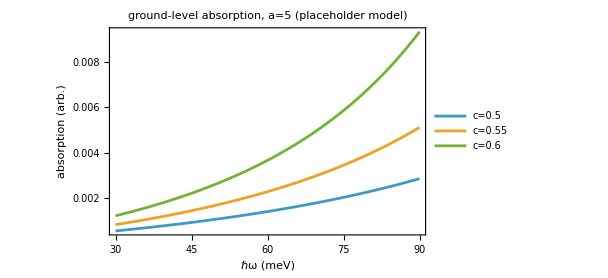

```mathematica
(* Figure 4/6 analog: absorption for the c-scan; Lorentzians at the X and
   XX->X lines. At zeroth order the two lines COINCIDE (Ebind = 0) -- the
   separation in the final figures is purely the variational correction. *)
absPreview[a_, c_][hw_] :=
  hw (gam/((hw - xMeV[a, c][0, 0])^2 + gam^2) +
     gam/((hw - (xxMeV[a, c][0, 0, 0, 0] - xMeV[a, c][0, 0] -
           ebindPh))^2 + gam^2));
Plot[Evaluate[Table[absPreview[5.0, cc][hw], {cc, {0.5, 0.55, 0.6}}]],
 {hw, 30, 90}, Frame -> True, PlotRange -> All,
 FrameLabel -> {"ℏω (meV)", "absorption (arb.)"},
 PlotLegends -> {"c=0.5", "c=0.55", "c=0.6"},
 PlotLabel -> "ground-level absorption, a=5 (placeholder model)",
 ImageSize -> 450]
```

## Findings / requirements for the real pipeline

1. Ebind and all XX->X vs X splittings are pure correlation effects: every optical figure depends on the variational corrections, zeroth order only fixes the overall energy scale and the geometry trends.
2. Excited-transition oscillator strengths vanish at zeroth order (orthogonal orbitals): the optics derivation must evaluate dipole matrix elements over the CORRELATED wavefunctions, which means new integrals per configuration -- add them to the production runners before the remaining geometries finish.
3. Linewidths hbar*Gamma are external: pick values (reference paper style) and state them in the paper.
4. Absolute photon energies need the gap Eg added; all preview plots are confinement energies only.

## Figure 1 analog: exciton and biexciton level diagram

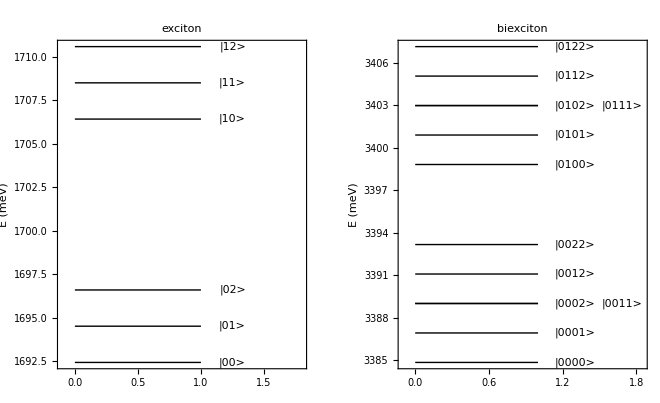

```mathematica
(* includeGap -> True shifts every level by (number of e-h pairs) x Eg:
   X by +Eg, XX by +2 Eg (total energies relative to the crystal ground
   state; recombination photons then come out as dE + Eg automatically).
   Default False = confinement energies, as in the reference paper. *)
includeGap = True;
gapMeV := If[TrueQ[includeGap], Eg ER2meV, 0];

xConfigs = Flatten[Table[{i, j}, {i, 0, 2}, {j, 0, 2}], 1];

(* label x-positions: stagger horizontally when consecutive levels are
   closer than ~a font height, so degenerate pairs don't overprint *)
labelX[vals_, x0_, dx_, tol_] :=
  Module[{prev = -Infinity, tog = 0},
   Table[
    If[vals[[n]] - prev < tol, tog = 1 - tog, tog = 0];
    prev = vals[[n]]; x0 + tog dx, {n, Length[vals]}]];

levelColumn[levels_, title_, x0_] :=
  Module[{vals = levels[[All, 1]], xs, tol},
   tol = 0.045 (Max[vals] - Min[vals]);
   xs = labelX[vals, x0, 0.38, tol];
   Graphics[{
     Table[{Thick, Line[{{0, vals[[n]]}, {1, vals[[n]]}}],
       Text[Style["|" <> StringJoin[ToString /@ levels[[n, 2]]] <> ">",
         11], {xs[[n]], vals[[n]]}]}, {n, Length[levels]}]},
    Frame -> {{True, False}, {False, False}},
    FrameLabel -> {None, "E (meV)"}, PlotLabel -> title,
    PlotRange -> {{-0.1, x0 + 0.55}, All}, AspectRatio -> 1.4]];

levelDiagram2[a_, c_, nX_: 6, nXX_: 12] :=
  Module[{lx, lxx},
   lx = SortBy[{xMeV[a, c] @@ # + gapMeV, #} & /@ xConfigs,
      First][[;; nX]];
   lxx = SortBy[{xxMeV[a, c] @@ # + 2 gapMeV, #} & /@ xxConfigs,
      First][[;; nXX]];
   GraphicsRow[{levelColumn[lx, "exciton", 1.25],
     levelColumn[lxx, "biexciton", 1.3]},
    PlotLabel->  Style[
      "Exciton and biexciton energy levels   (a=" <> ToString[a] <>
       " rB, c=" <> ToString[c] <> " rB" <>
       If[TrueQ[includeGap], ", gap included", ""] <> ")",
      Bold, 14],
    ImageSize -> 660]];

levelDiagram2[5.0, 0.5]
```

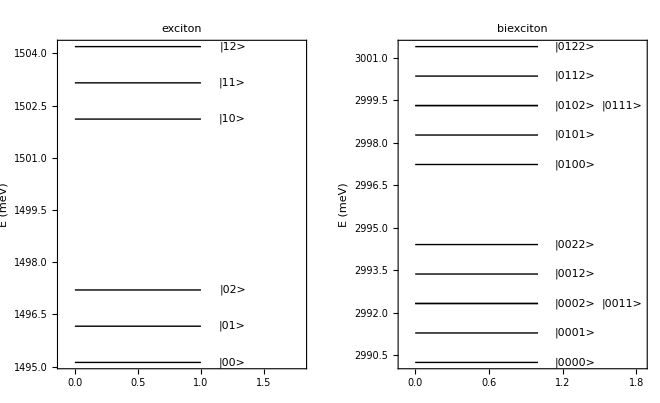

```mathematica
levelDiagram2[5.0, 1.0]
```

## Shifted geometry grid (paper-style nm values)

```mathematica
(* production grid defined in nm (round values as in the reference paper),
   converted to rB via the material Bohr radius from definitions.wl.
   The c-scan is shifted up from the paper's 5-6 nm for hard-wall validity:
   axial ground energy at c = 6 nm is ~156 meV, well below the ~260 meV
   GaAs/Al0.3Ga0.7As conduction-band offset. *)
nmToRB = 10.^-9/rB;
geomNm = {{50, 6}, {50, 7}, {50, 8}, {50, 10}, {40, 6}, {60, 6}};
geometries = nmToRB geomNm;

TableForm[
 Table[{geomNm[[k, 1]], geomNm[[k, 2]],
   NumberForm[geometries[[k, 1]], 4], NumberForm[geometries[[k, 2]], 4],
   NumberForm[Pi^2/geometries[[k, 2]]^2 ER2meV, 4],
   NumberForm[(xMeV @@ geometries[[k]])[0, 0], 5],
   NumberForm[(xMeV @@ geometries[[k]])[0, 1] -
     (xMeV @@ geometries[[k]])[0, 0], 3],
   NumberForm[(xMeV @@ geometries[[k]])[0, 0] + Eg ER2meV, 5]},
  {k, Length[geometries]}],
 TableHeadings -> {None,
   {"a (nm)", "c (nm)", "a (rB)", "c (rB)", "ϵz (meV)",
    "X00 (meV)", "h-spacing", "X00+Eg (meV)"}}]
```

```mathematica
(* level diagrams at the new base point and the thick-dome set *)
levelDiagram2 @@ geometries[[1]]
```

```mathematica
levelDiagram2 @@ geometries[[4]]
```

```mathematica
(* c-scan with the new grid marked (vertical gridlines at c = 6,7,8,10 nm) *)
Plot[{xMeV[geometries[[1, 1]], c][0, 0],
  xMeV[geometries[[1, 1]], c][0, 1], xMeV[geometries[[1, 1]], c][1, 0]},
 {c, 0.4, 1.1}, Frame -> True,
 GridLines -> {DeleteDuplicates[geometries[[All, 2]]], None},
 FrameLabel -> {"c (rB)", "E (meV)"},
 PlotLegends -> {"X00", "X01", "X10"},
 PlotLabel -> "a = 50 nm; gridlines mark the production c values",
 ImageSize -> 460]
```